```mathematica
items=Select[FindFullFormula[VertexDelete[Graph[plantri[[1]],VertexLabels->"Name"],1]],StringCount[SymbolName[#],"x"]==3&]
```

{v2cx36ax48bx579,v2ax36cx48bx579,v29bx37ax468x5c,v29bx37ax46cx58,v29bx357x4cx68a,v29bx35cx47x68a,v29bx357x46cx8a,v29bx35cx468x7a,v259x37ax48bx6c,v25cx37ax48bx69,v25cx37ax468x9b,v259x37ax46cx8b,v259x36cx48bx7a,v25cx36ax48bx79,v24bx3cx579x68a,v24cx3bx579x68a,v24cx36ax579x8b,v24bx36cx579x8a,v24cx357x68ax9b,v24bx35cx68ax79}

```mathematica
ShortSymb[s_]:=Select[Map[Select[#,!MemberQ[{2,3,4,5,6},#]&]&,SymbolToSets[s]],#≠{}&]
```

```mathematica
NotSymb[s_]:=Select[Map[Select[#,MemberQ[{2,3,4,5,6},#]&]&,SymbolToSets[s]],#≠{}&]
```

```mathematica
Sort[Gather[items,ShortSymb[#1]==ShortSymb[#2]&],Length[#1]<Length[#2]&]
```

{{v24bx35cx68ax79},{v24cx357x68ax9b},{v24cx36ax579x8b},{v24cx3bx579x68a},{v259x36cx48bx7a},{v259x37ax46cx8b},{v25cx37ax468x9b},{v25cx37ax48bx69},{v259x37ax48bx6c},{v29bx35cx468x7a},{v29bx35cx47x68a},{v29bx37ax46cx58},{v29bx37ax468x5c},{v2ax36cx48bx579},{v24bx3cx579x68a,v24bx36cx579x8a},{v29bx357x4cx68a,v29bx357x46cx8a},{v2cx36ax48bx579,v25cx36ax48bx79}}

```mathematica
Sort[Gather[items,NotSymb[#1]==NotSymb[#2]&],Length[#1]<Length[#2]&]
```

{{v24cx357x68ax9b,v24bx35cx68ax79},{v24cx36ax579x8b,v24bx36cx579x8a},{v24bx3cx579x68a,v24cx3bx579x68a},{v259x36cx48bx7a,v25cx36ax48bx79},{v25cx37ax468x9b,v259x37ax46cx8b},{v259x37ax48bx6c,v25cx37ax48bx69},{v29bx357x46cx8a,v29bx35cx468x7a},{v29bx357x4cx68a,v29bx35cx47x68a},{v29bx37ax468x5c,v29bx37ax46cx58},{v2cx36ax48bx579,v2ax36cx48bx579}}

```mathematica
repLight=Table[k->Style[k,Red,Bold],{k,{2,3,4,5,6}}]
```

{2→2,3→3,4→4,5→5,6→6}

```mathematica
Map[(SymbolToSets[#]/.repLight)&,{v2cx36ax48bx579,v25cx36ax48bx79}]
```

{{{2,12},{3,6,10},{4,8,11},{5,7,9}},{{2,5,12},{3,6,10},{4,8,11},{7,9}}}

```mathematica
TableForm[
Map[
Map[(SymbolToSets[#]/.repLight)&,#]&,
Sort[Gather[items,ShortSymb[#1]==ShortSymb[#2]&],Length[#1]<Length[#2]&]
]//Sort,TableDepth->2]
```

{{2,10},{3,6,12},{4,8,11},{5,7,9}} | 
{{2,9,11},{3,7,10},{4,6,8},{5,12}} | 
{{2,9,11},{3,7,10},{4,6,12},{5,8}} | 
{{2,9,11},{3,5,12},{4,7},{6,8,10}} | 
{{2,9,11},{3,5,12},{4,6,8},{7,10}} | 
{{2,4,11},{3,5,12},{6,8,10},{7,9}} | 
{{2,4,12},{3,11},{5,7,9},{6,8,10}} | 
{{2,4,12},{3,5,7},{6,8,10},{9,11}} | 
{{2,4,12},{3,6,10},{5,7,9},{8,11}} | 
{{2,5,9},{3,7,10},{4,8,11},{6,12}} | 
{{2,5,9},{3,7,10},{4,6,12},{8,11}} | 
{{2,5,9},{3,6,12},{4,8,11},{7,10}} | 
{{2,5,12},{3,7,10},{4,8,11},{6,9}} | 
{{2,5,12},{3,7,10},{4,6,8},{9,11}} | 
{{2,12},{3,6,10},{4,8,11},{5,7,9}} | {{2,5,12},{3,6,10},{4,8,11},{7,9}}
{{2,9,11},{3,5,7},{4,12},{6,8,10}} | {{2,9,11},{3,5,7},{4,6,12},{8,10}}
{{2,4,11},{3,12},{5,7,9},{6,8,10}} | {{2,4,11},{3,6,12},{5,7,9},{8,10}}

```mathematica
SymbolToSets[v29x37x4bx58x6cxa]/.repLight
```

{{2,9},{3,7},{4,11},{5,8},{6,12},{10}}

```mathematica
items[[1]]
```

v2x3x4x5x6x7x8x9xaxbxc

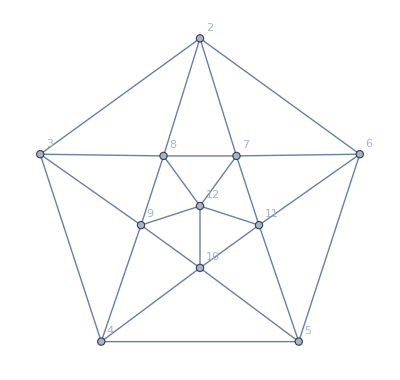

```mathematica
Graph[VertexDelete[Graph[plantri[[1]],VertexLabels->"Name"],1],GraphLayout->"TutteEmbedding"]
```

## Now for plantri 2

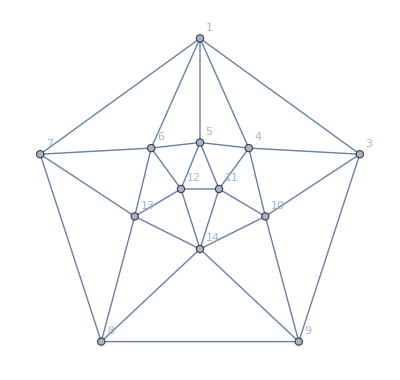

```mathematica
Graph[VertexDelete[Graph[plantri[[2]],VertexLabels->"Name"],2],GraphLayout->"TutteEmbedding"]
```

```mathematica
items=Select[FindFullFormula[VertexDelete[Graph[plantri[[2]],VertexLabels->"Name"],2]],StringCount[SymbolName[#],"x"]==3&]
```

{v1ex368bx479cx5ad,v1bdx36ex479cx58a,v1bdx357ex49cx68a,v1bdx35ex479cx68a,v1bdx357ex469x8ac,v1adx368bx49cx57e,v1acx368bx49dx57e,v1adx368bx479cx5e,v1acx368bx47ex59d,v1adx357ex49cx68b,v1acx357ex49dx68b,v1adx357ex48cx69b,v1adx35ex479cx68b,v1acx357ex468x9bd,v19bdx38cx46ex57a,v19bdx37cx46ex58a,v19bdx36ex48cx57a,v19cx368bx47ex5ad,v19bdx36ex47cx58a,v19bdx357ex4cx68a,v19bdx357ex48cx6a,v19bdx35ex47cx68a,v19bdx357x46ex8ac,v19bdx357ex468xac,v19bdx357ex46x8ac,v19bdx35ex468x7ac,v19bdx358x46ex7ac,v18acx3bdx46ex579,v18acx3bdx469x57e,v18acx37bx46ex59d,v18acx36bx49dx57e,v18bx36ex479cx5ad,v18acx36bx47ex59d,v18acx357ex4dx69b,v18acx357ex49dx6b,v18acx35dx47ex69b,v18acx357x46ex9bd,v18acx357ex469xbd,v18acx357ex46x9bd,v18acx35dx46ex79b}

```mathematica
ShortSymb[s_]:=Select[Map[Select[#,!MemberQ[{1,3,9,8,7},#]&]&,SymbolToSets[s]],#≠{}&]
```

```mathematica
NotSymb[s_]:=Select[Map[Select[#,MemberQ[{1,3,9,8,7},#]&]&,SymbolToSets[s]],#≠{}&]
```

```mathematica
repLight=Table[k->Style[k,Red,Bold],{k,{1,3,9,8,7}}]
```

{1→1,3→3,9→9,8→8,7→7}

```mathematica
TableForm[
Map[Framed[Column[#]]&,
Map[
Map[(SymbolToSets[#]/.repLight)->{Style[Length[NotSymb[#]],Darker[Green],Bold],NotSymb[#],ShortSymb[#]}&,#]&,
Sort[Gather[items,ShortSymb[#1]==ShortSymb[#2]&],Length[#1]<Length[#2]&]
]//Sort
],TableDepth->2]
```

{{1,14},{3,6,8,11},{4,7,9,12},{5,10,13}}→{3,{{1},{3,8},{7,9}},{{14},{6,11},{4,12},{5,10,13}}}
{{1,8,11},{3,6,14},{4,7,9,12},{5,10,13}}→{3,{{1,8},{3},{7,9}},{{11},{6,14},{4,12},{5,10,13}}}
{{1,9,12},{3,6,8,11},{4,7,14},{5,10,13}}→{3,{{1,9},{3,8},{7}},{{12},{6,11},{4,14},{5,10,13}}}
{{1,8,10,12},{3,5,13},{4,6,14},{7,9,11}}→{3,{{1,8},{3},{7,9}},{{10,12},{5,13},{4,6,14},{11}}}
{{1,8,10,12},{3,5,13},{4,7,14},{6,9,11}}→{4,{{1,8},{3},{7},{9}},{{10,12},{5,13},{4,14},{6,11}}}
{{1,8,10,12},{3,5,7},{4,6,14},{9,11,13}}→{3,{{1,8},{3,7},{9}},{{10,12},{5},{4,6,14},{11,13}}}
{{1,8,10,12},{3,11,13},{4,6,14},{5,7,9}}→{3,{{1,8},{3},{7,9}},{{10,12},{11,13},{4,6,14},{5}}}
{{1,8,10,12},{3,11,13},{4,6,9},{5,7,14}}→{4,{{1,8},{3},{9},{7}},{{10,12},{11,13},{4,6},{5,14}}}
{{1,8,10,12},{3,7,11},{4,6,14},{5,9,13}}→{3,{{1,8},{3,7},{9}},{{10,12},{11},{4,6,14},{5,13}}}
{{1,10,12},{3,6,8,11},{4,7,14},{5,9,13}}→{4,{{1},{3,8},{7},{9}},{{10,12},{6,11},{4,14},{5,13}}}
{{1,8,10,12},{3,6,11},{4,7,14},{5,9,13}}→{4,{{1,8},{3},{7},{9}},{{10,12},{6,11},{4,14},{5,13}}}
{{1,10,12},{3,6,8,11},{4,9,13},{5,7,14}}→{4,{{1},{3,8},{9},{7}},{{10,12},{6,11},{4,13},{5,14}}}
{{1,8,10,12},{3,6,11},{4,9,13},{5,7,14}}→{4,{{1,8},{3},{9},{7}},{{10,12},{6,11},{4,13},{5,14}}}
{{1,10,13},{3,6,8,11},{4,9,12},{5,7,14}}→{4,{{1},{3,8},{9},{7}},{{10,13},{6,11},{4,12},{5,14}}}
{{1,10,13},{3,6,8,11},{4,7,9,12},{5,14}}→{3,{{1},{3,8},{7,9}},{{10,13},{6,11},{4,12},{5,14}}}
{{1,9,11,13},{3,5,7},{4,6,14},{8,10,12}}→{3,{{1,9},{3,7},{8}},{{11,13},{5},{4,6,14},{10,12}}}
{{1,9,11,13},{3,5,8},{4,6,14},{7,10,12}}→{3,{{1,9},{3,8},{7}},{{11,13},{5},{4,6,14},{10,12}}}
{{1,9,11,13},{3,8,12},{4,6,14},{5,7,10}}→{3,{{1,9},{3,8},{7}},{{11,13},{12},{4,6,14},{5,10}}}
{{1,9,11,13},{3,7,12},{4,6,14},{5,8,10}}→{3,{{1,9},{3,7},{8}},{{11,13},{12},{4,6,14},{5,10}}}
{{1,10,12},{3,5,7,14},{4,6,8},{9,11,13}}→{4,{{1},{3,7},{8},{9}},{{10,12},{5,14},{4,6},{11,13}}}
{{1,8,10,12},{3,5,7,14},{4,6,9},{11,13}}→{3,{{1,8},{3,7},{9}},{{10,12},{5,14},{4,6},{11,13}}}
{{1,8,10,12},{3,5,7,14},{4,6},{9,11,13}}→{3,{{1,8},{3,7},{9}},{{10,12},{5,14},{4,6},{11,13}}}
{{1,10,12},{3,5,7,14},{4,9,13},{6,8,11}}→{4,{{1},{3,7},{9},{8}},{{10,12},{5,14},{4,13},{6,11}}}
{{1,8,10,12},{3,5,7,14},{4,13},{6,9,11}}→{3,{{1,8},{3,7},{9}},{{10,12},{5,14},{4,13},{6,11}}}
{{1,8,10,12},{3,5,7,14},{4,9,13},{6,11}}→{3,{{1,8},{3,7},{9}},{{10,12},{5,14},{4,13},{6,11}}}
{{1,10,13},{3,5,7,14},{4,9,12},{6,8,11}}→{4,{{1},{3,7},{9},{8}},{{10,13},{5,14},{4,12},{6,11}}}
{{1,10,13},{3,5,7,14},{4,8,12},{6,9,11}}→{4,{{1},{3,7},{8},{9}},{{10,13},{5,14},{4,12},{6,11}}}
{{1,10,13},{3,5,14},{4,7,9,12},{6,8,11}}→{4,{{1},{3},{7,9},{8}},{{10,13},{5,14},{4,12},{6,11}}}
{{1,11,13},{3,6,14},{4,7,9,12},{5,8,10}}→{4,{{1},{3},{7,9},{8}},{{11,13},{6,14},{4,12},{5,10}}}
{{1,9,11,13},{3,6,14},{4,8,12},{5,7,10}}→{4,{{1,9},{3},{8},{7}},{{11,13},{6,14},{4,12},{5,10}}}
{{1,9,11,13},{3,6,14},{4,7,12},{5,8,10}}→{4,{{1,9},{3},{7},{8}},{{11,13},{6,14},{4,12},{5,10}}}
{{1,11,13},{3,5,7,14},{4,6,9},{8,10,12}}→{4,{{1},{3,7},{9},{8}},{{11,13},{5,14},{4,6},{10,12}}}
{{1,9,11,13},{3,5,7,14},{4,6,8},{10,12}}→{3,{{1,9},{3,7},{8}},{{11,13},{5,14},{4,6},{10,12}}}
{{1,9,11,13},{3,5,7,14},{4,6},{8,10,12}}→{3,{{1,9},{3,7},{8}},{{11,13},{5,14},{4,6},{10,12}}}
{{1,9,11,13},{3,5,14},{4,6,8},{7,10,12}}→{4,{{1,9},{3},{8},{7}},{{11,13},{5,14},{4,6},{10,12}}}
{{1,11,13},{3,5,7,14},{4,9,12},{6,8,10}}→{4,{{1},{3,7},{9},{8}},{{11,13},{5,14},{4,12},{6,10}}}
{{1,11,13},{3,5,14},{4,7,9,12},{6,8,10}}→{4,{{1},{3},{7,9},{8}},{{11,13},{5,14},{4,12},{6,10}}}
{{1,9,11,13},{3,5,7,14},{4,12},{6,8,10}}→{3,{{1,9},{3,7},{8}},{{11,13},{5,14},{4,12},{6,10}}}
{{1,9,11,13},{3,5,7,14},{4,8,12},{6,10}}→{3,{{1,9},{3,7},{8}},{{11,13},{5,14},{4,12},{6,10}}}
{{1,9,11,13},{3,5,14},{4,7,12},{6,8,10}}→{4,{{1,9},{3},{7},{8}},{{11,13},{5,14},{4,12},{6,10}}}

```mathematica
ChromaticPolynomial[VertexDelete[Graph[plantri[[2]],VertexLabels->"Name"],2],4]/24
```

40

```mathematica
EmbedGraphInPlantri2[key_]:=Block[{val=allGraphs5[key], sets, reference={1,3,9,8,7}, g, sub},
sets=val["vertexsets"];
g=VertexDelete[ Graph[plantri[[2]]],2];
g=EdgeDelete[ g,{1<->3,3<->9,9<->8,8<->7,7<->1}];
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];

g
]
```

```mathematica
ShowGraph5Least[20746]
```

-Graphics-207464

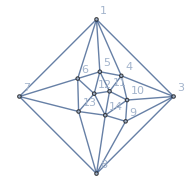

```mathematica
Graph[EmbedGraphInPlantri2[20746],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]
```

```mathematica
items2=Select[FindFullFormula[Graph[EmbedGraphInPlantri2[20746],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]],StringCount[SymbolName[#],"x"]==3&]
```

{v1bdx36ex479cx58a,v1bdx357ex49cx68a,v1bdx35ex479cx68a,v1bdx357ex469x8ac,v1adx357ex49cx68b,v1acx357ex49dx68b,v1adx357ex48cx69b,v1adx35ex479cx68b,v1acx357ex468x9bd,v19bdx37cx46ex58a,v19bdx36ex48cx57a,v19bdx36ex47cx58a,v19bdx357ex4cx68a,v19bdx357ex48cx6a,v19bdx35ex47cx68a,v19bdx357x46ex8ac,v19bdx357ex468xac,v19bdx357ex46x8ac,v19bdx35ex468x7ac,v18acx3bdx46ex579,v18acx3bdx469x57e,v18acx37bx46ex59d,v18acx36bx49dx57e,v18bx36ex479cx5ad,v18acx36bx47ex59d,v18acx357ex4dx69b,v18acx357ex49dx6b,v18acx35dx47ex69b,v18acx357x46ex9bd,v18acx357ex469xbd,v18acx357ex46x9bd,v18acx35dx46ex79b}

```mathematica
TableForm[
Map[Framed[Column[#]]&,
Map[
Map[(SymbolToSets[#]/.repLight)->{Style[Length[NotSymb[#]],Darker[Green],Bold],NotSymb[#],ShortSymb[#]}&,#]&,
Sort[Gather[items2,ShortSymb[#1]==ShortSymb[#2]&],Length[#1]<Length[#2]&]
]//Sort
],TableDepth->2]
```

{{1,8,11},{3,6,14},{4,7,9,12},{5,10,13}}→{3,{{1,8},{3},{7,9}},{{11},{6,14},{4,12},{5,10,13}}}
{{1,8,10,12},{3,5,13},{4,6,14},{7,9,11}}→{3,{{1,8},{3},{7,9}},{{10,12},{5,13},{4,6,14},{11}}}
{{1,8,10,12},{3,5,13},{4,7,14},{6,9,11}}→{4,{{1,8},{3},{7},{9}},{{10,12},{5,13},{4,14},{6,11}}}
{{1,8,10,12},{3,5,7},{4,6,14},{9,11,13}}→{3,{{1,8},{3,7},{9}},{{10,12},{5},{4,6,14},{11,13}}}
{{1,8,10,12},{3,6,11},{4,7,14},{5,9,13}}→{4,{{1,8},{3},{7},{9}},{{10,12},{6,11},{4,14},{5,13}}}
{{1,8,10,12},{3,6,11},{4,9,13},{5,7,14}}→{4,{{1,8},{3},{9},{7}},{{10,12},{6,11},{4,13},{5,14}}}
{{1,8,10,12},{3,11,13},{4,6,14},{5,7,9}}→{3,{{1,8},{3},{7,9}},{{10,12},{11,13},{4,6,14},{5}}}
{{1,8,10,12},{3,11,13},{4,6,9},{5,7,14}}→{4,{{1,8},{3},{9},{7}},{{10,12},{11,13},{4,6},{5,14}}}
{{1,8,10,12},{3,7,11},{4,6,14},{5,9,13}}→{3,{{1,8},{3,7},{9}},{{10,12},{11},{4,6,14},{5,13}}}
{{1,9,11,13},{3,5,7},{4,6,14},{8,10,12}}→{3,{{1,9},{3,7},{8}},{{11,13},{5},{4,6,14},{10,12}}}
{{1,9,11,13},{3,7,12},{4,6,14},{5,8,10}}→{3,{{1,9},{3,7},{8}},{{11,13},{12},{4,6,14},{5,10}}}
{{1,10,12},{3,5,7,14},{4,6,8},{9,11,13}}→{4,{{1},{3,7},{8},{9}},{{10,12},{5,14},{4,6},{11,13}}}
{{1,8,10,12},{3,5,7,14},{4,6,9},{11,13}}→{3,{{1,8},{3,7},{9}},{{10,12},{5,14},{4,6},{11,13}}}
{{1,8,10,12},{3,5,7,14},{4,6},{9,11,13}}→{3,{{1,8},{3,7},{9}},{{10,12},{5,14},{4,6},{11,13}}}
{{1,10,12},{3,5,7,14},{4,9,13},{6,8,11}}→{4,{{1},{3,7},{9},{8}},{{10,12},{5,14},{4,13},{6,11}}}
{{1,8,10,12},{3,5,7,14},{4,13},{6,9,11}}→{3,{{1,8},{3,7},{9}},{{10,12},{5,14},{4,13},{6,11}}}
{{1,8,10,12},{3,5,7,14},{4,9,13},{6,11}}→{3,{{1,8},{3,7},{9}},{{10,12},{5,14},{4,13},{6,11}}}
{{1,10,13},{3,5,7,14},{4,9,12},{6,8,11}}→{4,{{1},{3,7},{9},{8}},{{10,13},{5,14},{4,12},{6,11}}}
{{1,10,13},{3,5,7,14},{4,8,12},{6,9,11}}→{4,{{1},{3,7},{8},{9}},{{10,13},{5,14},{4,12},{6,11}}}
{{1,10,13},{3,5,14},{4,7,9,12},{6,8,11}}→{4,{{1},{3},{7,9},{8}},{{10,13},{5,14},{4,12},{6,11}}}
{{1,11,13},{3,6,14},{4,7,9,12},{5,8,10}}→{4,{{1},{3},{7,9},{8}},{{11,13},{6,14},{4,12},{5,10}}}
{{1,9,11,13},{3,6,14},{4,8,12},{5,7,10}}→{4,{{1,9},{3},{8},{7}},{{11,13},{6,14},{4,12},{5,10}}}
{{1,9,11,13},{3,6,14},{4,7,12},{5,8,10}}→{4,{{1,9},{3},{7},{8}},{{11,13},{6,14},{4,12},{5,10}}}
{{1,11,13},{3,5,7,14},{4,6,9},{8,10,12}}→{4,{{1},{3,7},{9},{8}},{{11,13},{5,14},{4,6},{10,12}}}
{{1,9,11,13},{3,5,7,14},{4,6,8},{10,12}}→{3,{{1,9},{3,7},{8}},{{11,13},{5,14},{4,6},{10,12}}}
{{1,9,11,13},{3,5,7,14},{4,6},{8,10,12}}→{3,{{1,9},{3,7},{8}},{{11,13},{5,14},{4,6},{10,12}}}
{{1,9,11,13},{3,5,14},{4,6,8},{7,10,12}}→{4,{{1,9},{3},{8},{7}},{{11,13},{5,14},{4,6},{10,12}}}
{{1,11,13},{3,5,7,14},{4,9,12},{6,8,10}}→{4,{{1},{3,7},{9},{8}},{{11,13},{5,14},{4,12},{6,10}}}
{{1,11,13},{3,5,14},{4,7,9,12},{6,8,10}}→{4,{{1},{3},{7,9},{8}},{{11,13},{5,14},{4,12},{6,10}}}
{{1,9,11,13},{3,5,7,14},{4,12},{6,8,10}}→{3,{{1,9},{3,7},{8}},{{11,13},{5,14},{4,12},{6,10}}}
{{1,9,11,13},{3,5,7,14},{4,8,12},{6,10}}→{3,{{1,9},{3,7},{8}},{{11,13},{5,14},{4,12},{6,10}}}
{{1,9,11,13},{3,5,14},{4,7,12},{6,8,10}}→{4,{{1,9},{3},{7},{8}},{{11,13},{5,14},{4,12},{6,10}}}

```mathematica
Length[items2]
```

32

```mathematica
items3=Select[FindFullFormula[Graph[EmbedGraphInPlantri2[23041],VertexLabels->"Name",GraphLayout->"TutteEmbedding"]],StringCount[SymbolName[#],"x"]==3&]
```

{v1ex36bx479cx5ad,v1adx36bx49cx57e,v1acx36bx49dx57e,v1adx36bx479cx5e,v1acx36bx47ex59d,v19cx36bx47ex5ad,v19bdx35x46ex7ac,v19bdx3cx46ex57a}

```mathematica
ShowGraph5Least[23041]
```

-Graphics-230411

```mathematica
TableForm[
Map[Framed[Column[#]]&,
Map[
Map[(SymbolToSets[#]/.repLight)->{Style[Length[NotSymb[#]],Darker[Green],Bold],NotSymb[#],ShortSymb[#]}&,#]&,
Sort[Gather[items3,ShortSymb[#1]==ShortSymb[#2]&],Length[#1]<Length[#2]&]
]//Sort
],TableDepth->2]
```

{{1,14},{3,6,11},{4,7,9,12},{5,10,13}}→{3,{{1},{3},{7,9}},{{14},{6,11},{4,12},{5,10,13}}}
{{1,10,12},{3,6,11},{4,7,14},{5,9,13}}→{4,{{1},{3},{7},{9}},{{10,12},{6,11},{4,14},{5,13}}}
{{1,10,12},{3,6,11},{4,9,13},{5,7,14}}→{4,{{1},{3},{9},{7}},{{10,12},{6,11},{4,13},{5,14}}}
{{1,9,12},{3,6,11},{4,7,14},{5,10,13}}→{3,{{1,9},{3},{7}},{{12},{6,11},{4,14},{5,10,13}}}
{{1,9,11,13},{3,5},{4,6,14},{7,10,12}}→{3,{{1,9},{3},{7}},{{11,13},{5},{4,6,14},{10,12}}}
{{1,9,11,13},{3,12},{4,6,14},{5,7,10}}→{3,{{1,9},{3},{7}},{{11,13},{12},{4,6,14},{5,10}}}
{{1,10,13},{3,6,11},{4,9,12},{5,7,14}}→{4,{{1},{3},{9},{7}},{{10,13},{6,11},{4,12},{5,14}}}
{{1,10,13},{3,6,11},{4,7,9,12},{5,14}}→{3,{{1},{3},{7,9}},{{10,13},{6,11},{4,12},{5,14}}}

```mathematica
Length[items3]
```

8